#### Mathieu equation stability, δ-ϵ.

x’’ + [δ + ϵ Cos(2t)]x = 0 - Mathieu equation

```mathematica
ClearAll[A,B,n];
Aπ[n_]:=Module[{temp},temp=DiagonalMatrix[Array[δ-4(#-1)^2&, n],0]+DiagonalMatrix[Array[ϵ/2&, n-1],1]+DiagonalMatrix[Array[ϵ/2&, n-1],-1];temp[[2,1]]=ϵ;
temp]


Bπ[n_]:=DiagonalMatrix[Array[δ-4(#)^2&, n],0]+DiagonalMatrix[Array[ϵ/2&, n-1],1]+DiagonalMatrix[Array[ϵ/2&, n-1],-1];


A2π[n_]:=Module[{temp},temp=DiagonalMatrix[Array[δ-(2#-1)^2&, n],0]+DiagonalMatrix[Array[ϵ/2&, n-1],1]+DiagonalMatrix[Array[ϵ/2&, n-1],-1];temp[[1,1]]+=ϵ/2;
temp]


B2π[n_]:=Module[{temp},temp=DiagonalMatrix[Array[δ-(2#-1)^2&, n],0]+DiagonalMatrix[Array[ϵ/2&, n-1],1]+DiagonalMatrix[Array[ϵ/2&, n-1],-1];temp[[1,1]]-=ϵ/2;
temp]
```

```mathematica
MatrixForm@Aπ[10]
MatrixForm@Bπ[4]
MatrixForm@A2π[4]
MatrixForm@B2π[4]
```

(δ | ϵ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ϵ | -4+δ | ϵ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ϵ/2 | -16+δ | ϵ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ϵ/2 | -36+δ | ϵ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ϵ/2 | -64+δ | ϵ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ϵ/2 | -100+δ | ϵ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ϵ/2 | -144+δ | ϵ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ϵ/2 | -196+δ | ϵ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ϵ/2 | -256+δ | ϵ/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ϵ/2 | -324+δ)

(-4+δ | ϵ/2 | 0 | 0
ϵ/2 | -16+δ | ϵ/2 | 0
0 | ϵ/2 | -36+δ | ϵ/2
0 | 0 | ϵ/2 | -64+δ)

(-1+δ+ϵ/2 | ϵ/2 | 0 | 0
ϵ/2 | -9+δ | ϵ/2 | 0
0 | ϵ/2 | -25+δ | ϵ/2
0 | 0 | ϵ/2 | -49+δ)

(-1+δ-ϵ/2 | ϵ/2 | 0 | 0
ϵ/2 | -9+δ | ϵ/2 | 0
0 | ϵ/2 | -25+δ | ϵ/2
0 | 0 | ϵ/2 | -49+δ)

#### Mathieu stability diagram

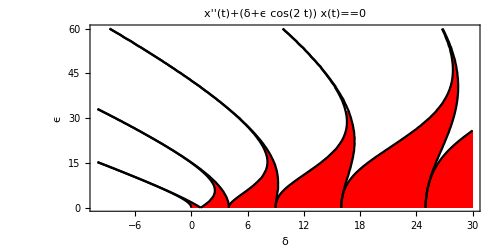

```mathematica
Show[
RegionPlot[
{
Det[A2π[15]]<=0&&Det[Aπ[15]]>=0,
Det[Aπ[15]]<=0&&Det[A2π[15]]>=0,
Det[B2π[15]]<=0&&Det[Bπ[15]]>=0,
Det[Bπ[15]]<=0&&Det[B2π[15]]>=0
},
{δ,-10,30},{ϵ,0,60},

MaxRecursion->6,
PlotStyle->Red,
BoundaryStyle->None,
PlotRangePadding->None,
FrameTicksStyle->Directive[Black,12],
FrameLabel->{Style["δ",16],Style["ϵ",16]},
PlotLabel->Style[Text@ToExpression["x''(t)+(\\delta + \\epsilon \\cos(2t))x(t)=0",TeXForm,HoldForm],16,Black],
ImageSize->{500,300},
AspectRatio->1/2
],

ContourPlot[{Det[Aπ[15]]==0,Det[Bπ[15]]==0,Det[A2π[15]]==0,Det[B2π[15]]==0},{δ,-10,30},{ϵ,0,60},ContourStyle->Black]
]
```

#### Spectrum of quantum particle in 1D cosine potential

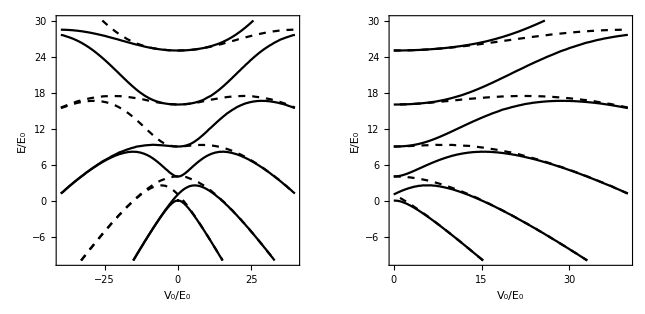

```mathematica
GraphicsRow@{Show[
ContourPlot[
{Det[Aπ[15]]==0,Det[B2π[15]]},{ϵ,-40,40} ,{δ,-10,30},
PlotRangePadding->None,
FrameTicksStyle->Directive[Black,12],
FrameLabel->{Style["V_0/E_0",16],Style["E/E_0",16]},
ContourStyle->Black
],
ContourPlot[
{Det[A2π[15]]==0,Det[Bπ[15]]},{ϵ,-40,40} ,{δ,-10,30},
PlotRangePadding->None,
FrameTicksStyle->Directive[Black,12],
FrameLabel->{Style["V_0/E_0",16],Style["E/E_0",16]},
ContourStyle->{{Black,Dashed}}
]
],
Show[
ContourPlot[
{Det[Aπ[15]]==0,Det[B2π[15]]},{ϵ,0,40} ,{δ,-10,30},
PlotRangePadding->None,
FrameTicksStyle->Directive[Black,12],
FrameLabel->{Style["V_0/E_0",16],Style["E/E_0",16]},
ContourStyle->Black
],
ContourPlot[
{Det[A2π[15]]==0,Det[Bπ[15]]},{ϵ,0,40} ,{δ,-10,30},
PlotRangePadding->None,
FrameTicksStyle->Directive[Black,12],
FrameLabel->{Style["V_0/E_0",16],Style["E/E_0",16]},
ContourStyle->{{Black,Dashed}}
]
]}
```

```mathematica
Export["/Users/goloshch/Desktop/Materials/Mathematica/Mathieu/Mathieu.pdf",EvaluationNotebook[]]
```

/Users/goloshch/Desktop/Materials/Mathematica/Mathieu/Mathieu.pdf